# PeterBurbery/UndirectedGraphs

Functions for undirected graphs

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ComputationonGraphs.nb"DocumentationEnglishGuidesComputationonGraphs.nb

"GraphConstructionandRepresentation.nb"DocumentationEnglishGuidesGraphConstructionandRepresentation.nb

"GraphFunctions.nb"DocumentationEnglishGuidesGraphFunctions.nb

"GraphOperationsandModifications.nb"DocumentationEnglishGuidesGraphOperationsandModifications.nb

"GraphPropertiesAndMeasurements.nb"DocumentationEnglishGuidesGraphPropertiesAndMeasurements.nb

"GraphVisualization.nb"DocumentationEnglishGuidesGraphVisualization.nb

"PathsCyclesandFlows.nb"DocumentationEnglishGuidesPathsCyclesandFlows.nb

"ReferencePages"

"Symbols"

"AlternatingTreeGraph.nb"DocumentationEnglishReferencePagesSymbolsAlternatingTreeGraph.nb

"BananaTreeGraph.nb"DocumentationEnglishReferencePagesSymbolsBananaTreeGraph.nb

"BookGraph.nb"DocumentationEnglishReferencePagesSymbolsBookGraph.nb

"CoboundaryPolynomial.nb"DocumentationEnglishReferencePagesSymbolsCoboundaryPolynomial.nb

"CombGraph.nb"DocumentationEnglishReferencePagesSymbolsCombGraph.nb

"FirecrackerGraph.nb"DocumentationEnglishReferencePagesSymbolsFirecrackerGraph.nb

"GearGraph.nb"DocumentationEnglishReferencePagesSymbolsGearGraph.nb

"GeneralizedTriangularGridGraph.nb"DocumentationEnglishReferencePagesSymbolsGeneralizedTriangularGridGraph.nb

"Girth.nb"DocumentationEnglishReferencePagesSymbolsGirth.nb

"GraphicalDegreeSequenceQ.nb"DocumentationEnglishReferencePagesSymbolsGraphicalDegreeSequenceQ.nb

"HelmGraph.nb"DocumentationEnglishReferencePagesSymbolsHelmGraph.nb

"IndependencePolynomial.nb"DocumentationEnglishReferencePagesSymbolsIndependencePolynomial.nb

"KayakPaddleGraph.nb"DocumentationEnglishReferencePagesSymbolsKayakPaddleGraph.nb

"LadderRungGraph.nb"DocumentationEnglishReferencePagesSymbolsLadderRungGraph.nb

"OriginalReferencePages"

"AlternatingTreeGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesAlternatingTreeGraph.nb

"BookGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesBookGraph.nb

"CombGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesCombGraph.nb

"FirecrackerGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesFirecrackerGraph.nb

"GearGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesGearGraph.nb

"Girth.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesGirth.nb

"KayakPaddleGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesKayakPaddleGraph.nb

"LadderRungGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesLadderRungGraph.nb

"PanGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesPanGraph.nb

"SunletGraph.nb"DocumentationEnglishReferencePagesSymbolsOriginalReferencePagesSunletGraph.nb

"PanGraph.nb"DocumentationEnglishReferencePagesSymbolsPanGraph.nb

"PositiveIntegerQ.nb"DocumentationEnglishReferencePagesSymbolsPositiveIntegerQ.nb

"RankPolynomial.nb"DocumentationEnglishReferencePagesSymbolsRankPolynomial.nb

"ReliabilityPolynomial.nb"DocumentationEnglishReferencePagesSymbolsReliabilityPolynomial.nb

"ResistanceMatrix.nb"DocumentationEnglishReferencePagesSymbolsResistanceMatrix.nb

"SunletGraph.nb"DocumentationEnglishReferencePagesSymbolsSunletGraph.nb

"TadpoleGraph.nb"DocumentationEnglishReferencePagesSymbolsTadpoleGraph.nb

"VertexCoordinateList.nb"DocumentationEnglishReferencePagesSymbolsVertexCoordinateList.nb

"VertexInsert.nb"DocumentationEnglishReferencePagesSymbolsVertexInsert.nb

"Tutorials"

"Kernel"

"AlternatingTreeGraph.wl"KernelAlternatingTreeGraph.wl

"BananaTreeGraph.wl"KernelBananaTreeGraph.wl

"BookGraph.wl"KernelBookGraph.wl

"CoboundaryPolynomial.wl"KernelCoboundaryPolynomial.wl

"CombGraph.wl"KernelCombGraph.wl

"FirecrackerGraph.wl"KernelFirecrackerGraph.wl

"GearGraph.wl"KernelGearGraph.wl

"GeneralizedTriangularGridGraph.wl"KernelGeneralizedTriangularGridGraph.wl

"Girth.wl"KernelGirth.wl

"GraphicalDegreeSequenceQ.wl"KernelGraphicalDegreeSequenceQ.wl

"HelmGraph.wl"KernelHelmGraph.wl

"IndependencePolynomial.wl"KernelIndependencePolynomial.wl

"KayakPaddleGraph.wl"KernelKayakPaddleGraph.wl

"LadderRungGraph.wl"KernelLadderRungGraph.wl

"PanGraph.wl"KernelPanGraph.wl

"PositiveIntegerQ.wl"KernelPositiveIntegerQ.wl

"RankPolynomial.wl"KernelRankPolynomial.wl

"ReliabilityPolynomial.wl"KernelReliabilityPolynomial.wl

"ResistanceMatrix.wl"KernelResistanceMatrix.wl

"SunletGraph.wl"KernelSunletGraph.wl

"TadpoleGraph.wl"KernelTadpoleGraph.wl

"UndirectedGraphs copy.wl"KernelUndirectedGraphs copy.wl

"UndirectedGraphs.wl"KernelUndirectedGraphs.wl

"VertexCoordinateList.wl"KernelVertexCoordinateList.wl

"VertexInsert.wl"KernelVertexInsert.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

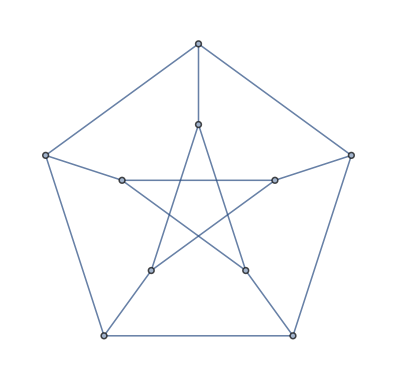

### Basic Description

Functions for undirected graphs.

### Details

Additional information about the paclet.

### Primary Context

MyPublisherID`MyPaclet`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Find the girth for the Petersen graph:

```mathematica
Girth[PetersenGraph[]]
```

5

Is this a graphical degree sequence:

```mathematica
GraphicalDegreeSequenceQ[{2,2,2,1,1}]
```

True

Make a random graph:

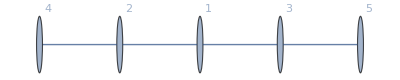

```mathematica
RandomGraph[DegreeGraphDistribution[{2,2,2,1,1}],VertexLabels->"Name"]
```

Make another random graph:

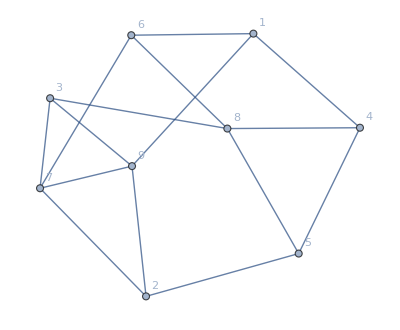

```mathematica
RandomGraph[DegreeGraphDistribution[{3,3,3,3,3,3,4,4,4}],VertexLabels->"Name"]
```

Is this a graphical degree sequence:

```mathematica
GraphicalDegreeSequenceQ[{1,3,3,3,5,6,6}]
```

False

Make an alternating tree graph:

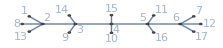

```mathematica
AlternatingTreeGraph[7,VertexLabels->"Name"]
```

Make a firecracker graph:

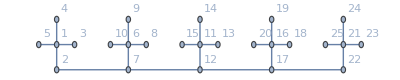

```mathematica
FirecrackerGraph[{5,5},VertexLabels->"Name"]
```

### Scope

## Source & Additional Information

### Creator

Peter Cullen Burbery

### Source Control Repository

https://github.com/PeterCullenBurbery/undirected-graphs-paclet/tree/main/Undirected%20Graphs

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Graph theory

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

EulerizeGraph

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes